```mathematica
(*Base kets and basic operators definition*)
Subscript[ket, 0]={{1},{0}};
Subscript[ket, 1]={{0},{1}};
Id=IdentityMatrix[2];
X=PauliMatrix[1];
Y=PauliMatrix[2];
Z=PauliMatrix[3];
H=HadamardMatrix[2];
Subscript[P, 0]=Subscript[ket, 0].ConjugateTranspose[Subscript[ket, 0]];
Subscript[P, 1]=Subscript[ket, 1].ConjugateTranspose[Subscript[ket, 1]];
R[ϕ_]:=Subscript[P, 0] + ⅇ^(ⅈ ϕ) Subscript[P, 1];
CNOT=KroneckerProduct[Subscript[P, 0],Id]+KroneckerProduct[Subscript[P, 1],X];
CR[ϕ_]:=KroneckerProduct[Subscript[P, 0],Id]+KroneckerProduct[Subscript[P, 1],R[ϕ]];
CR13[ϕ_]:=KroneckerProduct[Subscript[P, 0],Id,Id]+KroneckerProduct[Subscript[P, 1],Id,R[ϕ]];
ρ[ψ_]:=ψ.ConjugateTranspose[ψ];
```

{{{0.0428145+0. ⅈ}},{{0.0303536+0. ⅈ}},{{0.0927012+0. ⅈ}},{{0.834131+0. ⅈ}}}

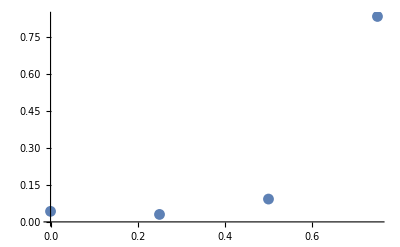

0.679537+0. ⅈ

```mathematica
(*Quantum phase estimation algorithm for 1 qubit operators with 2 qubits of precision - Version a*)
Subscript[ket, 0]={{1},{0}};
Subscript[ket, 1]={{0},{1}};
Id=IdentityMatrix[2];
X=PauliMatrix[1];
Y=PauliMatrix[2];
Z=PauliMatrix[3];
H=HadamardMatrix[2];
Subscript[P, 0]=Subscript[ket, 0].ConjugateTranspose[Subscript[ket, 0]];
Subscript[P, 1]=Subscript[ket, 1].ConjugateTranspose[Subscript[ket, 1]];
R[ϕ_]:=Subscript[P, 0] + ⅇ^(ⅈ ϕ) Subscript[P, 1];
CNOT=KroneckerProduct[Subscript[P, 0],Id]+KroneckerProduct[Subscript[P, 1],X];
CR[ϕ_]:=KroneckerProduct[Subscript[P, 0],Id]+KroneckerProduct[Subscript[P, 1],R[ϕ]];
CR13[ϕ_]:=KroneckerProduct[Subscript[P, 0],Id,Id]+KroneckerProduct[Subscript[P, 1],Id,R[ϕ]];
ρ[ψ_]:=ψ.ConjugateTranspose[ψ];

ψ0=KroneckerProduct[Subscript[ket, 0],Subscript[ket, 0]];
ψ0=KroneckerProduct[H,H].ψ0;
ψ=Subscript[ket, 1];
p=0.69;
U=R[2π p];
ψt=KroneckerProduct[ψ0,ψ];

ψt=(KroneckerProduct[Id,Subscript[P, 0],Id]+KroneckerProduct[Id,Subscript[P, 1],U]).ψt;

ψt=(KroneckerProduct[Subscript[P, 0],Id,Id]+KroneckerProduct[Subscript[P, 1],Id,U]).ψt;
ψt=(KroneckerProduct[Subscript[P, 0],Id,Id]+KroneckerProduct[Subscript[P, 1],Id,U]).ψt;

(*Inverse QFT*)
ψt=KroneckerProduct[{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}},Id].ψt;
ψt=KroneckerProduct[Id,H,Id].ψt;
ψt=(KroneckerProduct[Id,Subscript[P, 0],Id]+KroneckerProduct[R[(-2π)/2^2],Subscript[P, 1],Id]).ψt;
ψt=KroneckerProduct[H,Id,Id].ψt;

ψt0=KroneckerProduct[Subscript[P, 0],Subscript[P, 0],Id].ψt;
ψt1=KroneckerProduct[Subscript[P, 0],Subscript[P, 1],Id].ψt;
ψt2=KroneckerProduct[Subscript[P, 1],Subscript[P, 0],Id].ψt;
ψt3=KroneckerProduct[Subscript[P, 1],Subscript[P, 1],Id].ψt;
{FullSimplify[ConjugateTranspose[ψt0].ψt0],FullSimplify[ConjugateTranspose[ψt1].ψt1],FullSimplify[ConjugateTranspose[ψt2].ψt2],FullSimplify[ConjugateTranspose[ψt3].ψt3]}
ListPlot[Table[{N[(i-1)/2^2],{FullSimplify[ConjugateTranspose[ψt0].ψt0],FullSimplify[ConjugateTranspose[ψt1].ψt1],FullSimplify[ConjugateTranspose[ψt2].ψt2],FullSimplify[ConjugateTranspose[ψt3].ψt3]}[[i,1,1]]},{i,1,4}],PlotRange->All]
ExpectedVal=Sum[N[(i-1)/2^2] {FullSimplify[ConjugateTranspose[ψt0].ψt0],FullSimplify[ConjugateTranspose[ψt1].ψt1],FullSimplify[ConjugateTranspose[ψt2].ψt2],FullSimplify[ConjugateTranspose[ψt3].ψt3]}[[i,1,1]],{i,1,4}]
```

```mathematica
(*Quantum phase estimation algorithm for 1 qubit operators with 2 qubits of precision - Version b*)
Subscript[ket, 0]={{1},{0}};
Subscript[ket, 1]={{0},{1}};
Id=IdentityMatrix[2];
X=PauliMatrix[1];
Y=PauliMatrix[2];
Z=PauliMatrix[3];
H=HadamardMatrix[2];
Subscript[P, 0]=Subscript[ket, 0].ConjugateTranspose[Subscript[ket, 0]];
Subscript[P, 1]=Subscript[ket, 1].ConjugateTranspose[Subscript[ket, 1]];
R[ϕ_]:=Subscript[P, 0] + ⅇ^(ⅈ ϕ) Subscript[P, 1];
CNOT=KroneckerProduct[Subscript[P, 0],Id]+KroneckerProduct[Subscript[P, 1],X];
CR[ϕ_]:=KroneckerProduct[Subscript[P, 0],Id]+KroneckerProduct[Subscript[P, 1],R[ϕ]];
CR13[ϕ_]:=KroneckerProduct[Subscript[P, 0],Id,Id]+KroneckerProduct[Subscript[P, 1],Id,R[ϕ]];
ρ[ψ_]:=ψ.ConjugateTranspose[ψ];

ψ0=KroneckerProduct[Subscript[ket, 0],Subscript[ket, 0]];
ψ0=KroneckerProduct[H,H].ψ0;
ψ=Subscript[ket, 1];
p=0.69;
U=R[2π p];
ψt=KroneckerProduct[ψ0,ψ];


ψt=(KroneckerProduct[Id,Subscript[P, 0],Id]+KroneckerProduct[Id,Subscript[P, 1],U]).ψt;

ψt=(KroneckerProduct[Subscript[P, 0],Id,Id]+KroneckerProduct[Subscript[P, 1],Id,U]).ψt;
ψt=(KroneckerProduct[Subscript[P, 0],Id,Id]+KroneckerProduct[Subscript[P, 1],Id,U]).ψt;


(*Inverse QFT*)
ψt=KroneckerProduct[ConjugateTranspose[FourierMatrix[4]],Id].ψt;

ψt0=KroneckerProduct[Subscript[P, 0],Subscript[P, 0],Id].ψt;
ψt1=KroneckerProduct[Subscript[P, 0],Subscript[P, 1],Id].ψt;
ψt2=KroneckerProduct[Subscript[P, 1],Subscript[P, 0],Id].ψt;
ψt3=KroneckerProduct[Subscript[P, 1],Subscript[P, 1],Id].ψt;
{FullSimplify[ConjugateTranspose[ψt0].ψt0],FullSimplify[ConjugateTranspose[ψt1].ψt1],FullSimplify[ConjugateTranspose[ψt2].ψt2],FullSimplify[ConjugateTranspose[ψt3].ψt3]}
ListPlot[Table[{N[(i-1)/2^2],{FullSimplify[ConjugateTranspose[ψt0].ψt0],FullSimplify[ConjugateTranspose[ψt1].ψt1],FullSimplify[ConjugateTranspose[ψt2].ψt2],FullSimplify[ConjugateTranspose[ψt3].ψt3]}[[i,1,1]]},{i,1,4}],PlotRange->All]
ExpectedVal=Sum[N[(i-1)/2^2] {FullSimplify[ConjugateTranspose[ψt0].ψt0],FullSimplify[ConjugateTranspose[ψt1].ψt1],FullSimplify[ConjugateTranspose[ψt2].ψt2],FullSimplify[ConjugateTranspose[ψt3].ψt3]}[[i,1,1]],{i,1,4}]
```

{{{0.0428145+0. ⅈ}},{{0.0303536+0. ⅈ}},{{0.0927012+0. ⅈ}},{{0.834131+0. ⅈ}}}

-Graphics-

0.679537+0. ⅈ

{{1.+0. ⅈ}}

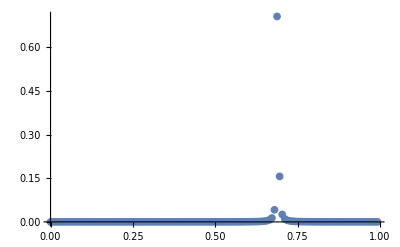

0.687638+0. ⅈ

-0.00236184+0. ⅈ

-0.343472+0. ⅈ

-0.342296+0. ⅈ

```mathematica
(*Quantum phase estimation algorithm for 1 qubit operators with 7 qubits ancilla - Version b*)

Subscript[ket, 0]={{1},{0}};
Subscript[ket, 1]={{0},{1}};
Id=IdentityMatrix[2];
X=PauliMatrix[1];
Y=PauliMatrix[2];
Z=PauliMatrix[3];
H=HadamardMatrix[2];
Subscript[P, 0]=Subscript[ket, 0].ConjugateTranspose[Subscript[ket, 0]];
Subscript[P, 1]=Subscript[ket, 1].ConjugateTranspose[Subscript[ket, 1]];
R[ϕ_]:=Subscript[P, 0] + ⅇ^(ⅈ ϕ) Subscript[P, 1];
CNOT=KroneckerProduct[Subscript[P, 0],Id]+KroneckerProduct[Subscript[P, 1],X];
CR[ϕ_]:=KroneckerProduct[Subscript[P, 0],Id]+KroneckerProduct[Subscript[P, 1],R[ϕ]];
CR13[ϕ_]:=KroneckerProduct[Subscript[P, 0],Id,Id]+KroneckerProduct[Subscript[P, 1],Id,R[ϕ]];
ρ[ψ_]:=ψ.ConjugateTranspose[ψ];

ψ0=KroneckerProduct[Subscript[ket, 0],Subscript[ket, 0],Subscript[ket, 0],Subscript[ket, 0],Subscript[ket, 0],Subscript[ket, 0],Subscript[ket, 0]];
ψ0=N[KroneckerProduct[H,H,H,H,H,H,H].ψ0];
ψ=Subscript[ket, 0];
p=0.69;
ϕ=2π p;
θ=(1.01*2π)/4;
U=N[{{ⅇ^(ⅈ ϕ),0},{0,ⅇ^(ⅈ θ)}}];
ψt=N[KroneckerProduct[ψ0,ψ]];

ψt=N[(KroneckerProduct[Id,Id,Id,Id,Id,Id,Subscript[P, 0],Id]+KroneckerProduct[Id,Id,Id,Id,Id,Id,Subscript[P, 1],U]).ψt];
ψt=N[(KroneckerProduct[Id,Id,Id,Id,Id,Subscript[P, 0],Id,Id]+KroneckerProduct[Id,Id,Id,Id,Id,Subscript[P, 1],Id,MatrixPower[U,2]]).ψt];
ψt=N[(KroneckerProduct[Id,Id,Id,Id,Subscript[P, 0],Id,Id,Id]+KroneckerProduct[Id,Id,Id,Id,Subscript[P, 1],Id,Id,MatrixPower[U,2^2]]).ψt];
ψt=N[(KroneckerProduct[Id,Id,Id,Subscript[P, 0],Id,Id,Id,Id]+KroneckerProduct[Id,Id,Id,Subscript[P, 1],Id,Id,Id,MatrixPower[U,2^3]]).ψt];
ψt=N[(KroneckerProduct[Id,Id,Subscript[P, 0],Id,Id,Id,Id,Id]+KroneckerProduct[Id,Id,Subscript[P, 1],Id,Id,Id,Id,MatrixPower[U,2^4]]).ψt];
ψt=N[(KroneckerProduct[Id,Subscript[P, 0],Id,Id,Id,Id,Id,Id]+KroneckerProduct[Id,Subscript[P, 1],Id,Id,Id,Id,Id,MatrixPower[U,2^5]]).ψt];
ψt=N[(KroneckerProduct[Subscript[P, 0],Id,Id,Id,Id,Id,Id,Id]+KroneckerProduct[Subscript[P, 1],Id,Id,Id,Id,Id,Id,MatrixPower[U,2^6]]).ψt];




(*Inverse QFT*)
ψt=N[KroneckerProduct[ConjugateTranspose[FourierMatrix[2^7]],Id].ψt];


For[i=0,i<128,i++,sub0=Mod[i,2];sub1=Which[i==0,0,Mod[i,2]==0&&sub1==0,1,Mod[i,2]==0&&sub1==1,0,True,sub1];sub2=Which[i==0,0,Mod[i,2^2]==0&&sub2==0,1,Mod[i,2^2]==0&&sub2==1,0,True,sub2];sub3=Which[i==0,0,Mod[i,2^3]==0&&sub3==0,1,Mod[i,2^3]==0&&sub3==1,0,True,sub3];sub4=Which[i==0,0,Mod[i,2^4]==0&&sub4==0,1,Mod[i,2^4]==0&&sub4==1,0,True,sub4];sub5=Which[i==0,0,Mod[i,2^5]==0&&sub5==0,1,Mod[i,2^5]==0&&sub5==1,0,True,sub5];sub6=Which[i==0,0,Mod[i,2^6]==0&&sub6==0,1,Mod[i,2^6]==0&&sub6==1,0,True,sub6];Subscript[ψt, i]=N[KroneckerProduct[Subscript[P, sub6],Subscript[P, sub5],Subscript[P, sub4],Subscript[P, sub3],Subscript[P, sub2],Subscript[P, sub1],Subscript[P, sub0],Id].ψt];Subscript[ψt, i]=N[ConjugateTranspose[Subscript[ψt, i]].Subscript[ψt, i]];]

L=Table[{i,N[i/2^7],Subscript[ψt, i][[1,1]]},{i,0,127}];
Sum[Subscript[ψt, i],{i,0,127}]
ListPlot[Table[{N[i/2^7],Subscript[ψt, i][[1,1]]},{i,0,127}],PlotRange->All]
ExpectedVal=Sum[L[[i,2]] L[[i,3]],{i,2,128}]
Err=ExpectedVal-p
Errp=(100 Err)/ExpectedVal
Errp2=(100 Err)/p
```

```mathematica
KroneckerProduct[H,Id].(KroneckerProduct[Id,Subscript[P, 0]]+KroneckerProduct[R[(-2π)/2^2],Subscript[P, 1]]).KroneckerProduct[Id,H].{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}}-FullSimplify[ConjugateTranspose[FourierMatrix[2^2]]]//MatrixForm
FullSimplify[{{1,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0},{0,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,1}}.KroneckerProduct[Id,Id,H].(KroneckerProduct[Id,Id,Subscript[P, 0]]+KroneckerProduct[Id,R[(2π)/2^2],Subscript[P, 1]]).KroneckerProduct[Id,H,Id].(KroneckerProduct[Id,Id,Subscript[P, 0]]+KroneckerProduct[R[(2π)/2^3],Id,Subscript[P, 1]]).(KroneckerProduct[Id,Subscript[P, 0],Id]+KroneckerProduct[R[(2π)/2^2],Subscript[P, 1],Id]).KroneckerProduct[H,Id,Id]-
FourierMatrix[2^3]]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)